## Fourier Series

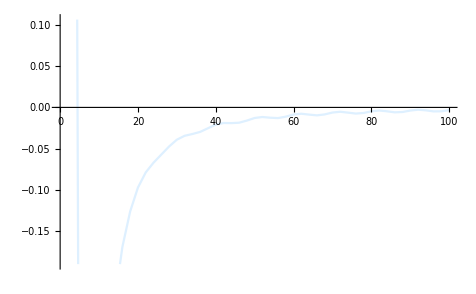

```mathematica
fbas[x_] :=  E^-x Sin[2 Pi x]  + 0.5 + Piecewise[{{0.2,0.6≤x<0.63}},0];
Plot[fbas[x],{x,0,1},AxesLabel->{"x","f[x]"},PlotStyle->Thickness[0.004]];
ncoeffmax = 100;
L = Pi;
calcoeff := Module[{},a[0]=(1.0/(2L)) NIntegrate[fbas[x],{x,-L,L},AccuracyGoal->8];b[0]=0.0;Do[(a[n]=(1.0/L) NIntegrate[fbas[x] Cos[n Pi x/L],{x,-L,L},AccuracyGoal->8];
b[n]=(1.0/L) NIntegrate[fbas[x] Sin[n Pi x/L],{x,-L,L},AccuracyGoal->8]),{n,1,ncoeffmax}]]
calcoeff
Do[(analyta[n]=0;analytb[n]=If[EvenQ[n],0,4.0/(n Pi)]),{n,0,ncoeffmax}];
p1 = ListPlot[Table[{n,a[n]},{n,0,ncoeffmax,2}],PlotStyle->LightBlue,Joined->True]
```

```mathematica
fbas[x_] :=  E^-x Sin[2 Pi x]  + 0.5;
Plot[fbas[x],{x,0,1},AxesLabel->{"x","f[x]"},PlotStyle->Thickness[0.004]];
ncoeffmax = 100;
L = Pi;
calcoeff := Module[{},a[0]=(1.0/(2L)) NIntegrate[fbas[x],{x,-L,L},AccuracyGoal->8];b[0]=0.0;Do[(a[n]=(1.0/L) NIntegrate[fbas[x] Cos[n Pi x/L],{x,-L,L},AccuracyGoal->8];
b[n]=(1.0/L) NIntegrate[fbas[x] Sin[n Pi x/L],{x,-L,L},AccuracyGoal->8]),{n,1,ncoeffmax}]]
calcoeff
Do[(analyta[n]=0;analytb[n]=If[EvenQ[n],0,4.0/(n Pi)]),{n,0,ncoeffmax}];
p2 = ListPlot[Table[{n,a[n]},{n,0,ncoeffmax,2},PlotRange->{-0.15,0}],PlotStyle->Orange]
```

Table::nliter: Non-list iterator PlotRange→{-0.15,0} at position 3 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator PlotRange→{-0.15,0.} at position 3 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

ListPlot::lpn: Table[{n,a[n]},{n,0.,ncoeffmax,2.},PlotRange→{-0.15,0.}] is not a list of numbers or pairs of numbers.

ListPlot[Table[{n,a[n]},{n,0,ncoeffmax,2},PlotRange→{-0.15,0}],PlotStyle→RGBColor[1, 0.5, 0]]

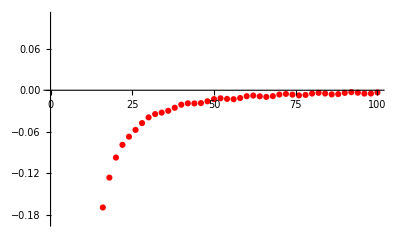

```mathematica
p2 = ListPlot[Table[{n,a[n]},{n,0,ncoeffmax,2}],PlotStyle->Red]
```

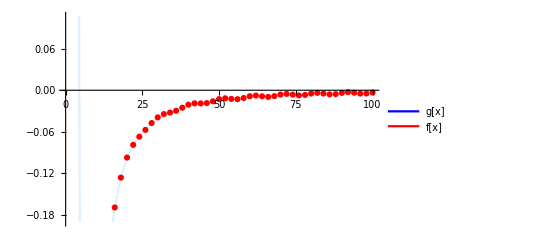

```mathematica
Legended[Show[{p1,p2}],LineLegend[{Blue,Red},{"g[x]","f[x]"}]]
```

## Haar Waveletsp